```mathematica
(* Potential, without normalization *)
V[θ_] =θ^2; (*θ is now ϕ/μ*)

(* Putting in required known constants *)
m = 1.2209*10^28 ; (*Non-reduced Planck Mass, Subscript[m, pl], in eV/c^2 *)
Mmin = 0.5; (*M is Subscript[m, pl]/μ *)
Mmax = 2;
wmin=-1/3; (*most conservative lower bound on w*)
wmax = 1; (*most conservative upper bound on w*)
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)

(* Slow-roll parameters *)
ϵ[θ_,M_] := M^2/(16 π)(V'[θ]/V[θ])^2
η[θ_,M_] = M^2/(16 π)(V''[θ]/V[θ]) 

ξ[ θ_,M_] = M^4/(16^2 π^2)((V'[θ] V'''[θ])/(V[θ])^2)

σ[ θ_,M_] = 2 η[θ,M] - 4 ϵ[θ,M]

(* Field Value at the end of inflation *)
θe[M_] := Re[X/. FindRoot[ϵ[X,M]==1,{X,M/√π}]]
Nume[θ_?NumberQ,M_]:=Re[(8 π/M^2) NIntegrate[V[b]/V'[b],{b, θe[M],θ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
θN[NN_,M_] := Re[xx/. FindRoot[Nume[xx,M] == NN, {xx,θe[M]}]]

(* Observables *)
CC = 0.0814514
r[NN_,M_] := Re[16.0ϵ[θN[NN,M],M] (1 - CC ( σ[θN[NN,M],M] + 2 ϵ[θN[NN,M],M]))]
n[NN_,M_] := Re[1 + σ[θN[NN,M],M] - (5 - 3 CC) ϵ[θN[NN,M],M]^2 - 1/4(3 - 5 CC) σ[θN[NN,M],M] ϵ[θN[NN,M],M] + 1/2 (3 - CC) ξ [θN[NN,M],M]]

(* Normalization *)
Vend[NN_,M_]:= (3 δ^2 M^2)/(128π)(V'[θN[NN,M]]/V[θN[NN,M]])^2(V[θe[M]]/V[θN[NN,M]])
V0[NN_,M_]:= (3 δ^2 M^2)/(128π)(V'[θN[NN,M]]/V[θN[NN,M]])^2(1/V[θN[NN,M]]) (*This is my normalization coefficient*)
HN[NN_,M_]:=m*√((8 π)/(3 M^2)V0[NN,M]*V[θN[NN,M]]) (*Normalized and correct Hk--the extra m in front is because I had forgotten for a while that there is an mpl factor that I had dropped everywhere, since it wound up cancelling/dropping in the end because the first method for Nk has log Trh/mpl, but I need the mpl here. Anyway, I can simplify, but somehow that results in complex answers, whereas this way I get real ones, so...not simplifying.*)

(*Known Parameters*)
Ωmh2 = 0.14212;
aeq=(4.15*10^-5)/Ωmh2; (*I'm actually not sure what to make of this, because I get something like 3.5*10^-4 this way, but if I go by zeq, I get that aeq should be about 2.9*10^-4. I'm not at all sure if this matters, though. *)
a0 = 1; (*I'm pretty sure I can say this*)
H0 = 67.26*3.241*10^-20*6.58*10^-16; (*Converting from km/s/Mpc to eV*)
Ωm = 0.316; (*This appears to be the most recent Planck number*)
Heq = (2Ωm*H0^2*aeq^-3)^(1/2); (*From an equation for H(y), found here: http://www.tapir.caltech.edu/~chirata/ph217/lec06.pdf *)
pivotk = 3.2*10^-31; (*0.05 Mpc^-1 in eV*)

(*Insert calculation for NRD here*)

NRD = 11.513; (*I manually found y of nucleosynthesis [y is a/aeq] from the t[y] formula, then took the log of that, since the paper says NRD = ln[aeq/are]. Whether or not this is an accurate way to estimate NRD, the fact is that the paper started out with the ratio of a's, so doing it differently would be foolish. *)

(*Getting Nre from the foregoing*)
Nre[NN_,M_]:=-NN-NRD+Log[(aeq*Heq)/(a0*H0)]+Log[HN[NN,M]/Heq]-Log[pivotk/(a0*H0)]
knowns = -NRD+Log[(aeq*Heq)/pivotk](*Simplified a bit*)
(* Reheat Temperature *)
Trh[NN_,M_,w_]:=m*Exp[-3/4(1+w)Nre[NN,M]](3/π^2)^(1/4)(1+1/2)^(1/4)Vend[NN,M]^(1/4)
(* Min N *)
Nm2[M_,w_]:= Re[xyy/. FindRoot[Trh[xyy,M,w]==50000,{xyy,45}]](*Method 2, appears to be working!*)
```

M^2/(8 π θ^2)

0

-(3 M^2)/(4 π θ^2)

0.0814514

-13.0807

```mathematica
Nm2[1,1/3]
Nre[Nm2[1,1/3],1]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

57.3945

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

46.0303

```mathematica
ParametricPlot[{{n[Nk,1],Trh[Nk,1,1/3]},{n[Nk,1],Trh[Nk,1,0]},{n[Nk,1],Trh[Nk,1,-1/3]},{n[Nk,1],Trh[Nk,1,1]},{n[Nk,1],Trh[Nk,1,0.25]}},{Nk,30,75},AspectRatio->2,PlotRange->{{0.95,0.98},{0,10^12}}, PlotLegends->"Expressions"]
```

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {2.86354}.

ReplaceAll::reps: {FindRoot[Nume[xx,5]==Nk,{xx,θe[5]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {2.86354}.

ReplaceAll::reps: {FindRoot[Nume[xx,5]==Nk,{xx,θe[5]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {2.86354}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,5]==Nk,{xx,θe[5]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

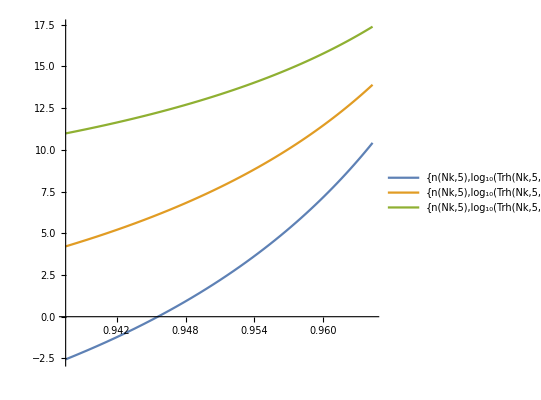

```mathematica
ParametricPlot[{{n[Nk,5],Log10[Trh[Nk,5,1/3]]},{n[Nk,5],Log10[Trh[Nk,5,0]]},{n[Nk,5],Log10[Trh[Nk,5,-1/3]]}},{Nk,40,70},AspectRatio->1,PlotLegends->"Expressions"]
```

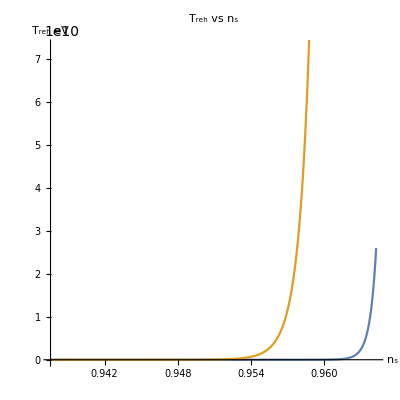

```mathematica
Show[%23,AxesLabel->{HoldForm[Subscript[n, s]],HoldForm[Subscript[T, reh] eV]},PlotLabel->HoldForm[Subscript[T, reh] vs Subscript[n, s]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
(*Behavioral Checks*)
(*Plot[Nre[Nk,1],{Nk,40,60}]*)
Plot[{Trh[Nk,1,-1/3],Trh[Nk,1,0],Trh[Nk,1,1/3],Trh[Nk,1,1]},{Nk,40,60}]
(*Plot[Nm2[1,w],{w,wmin,wmax}]*)
```

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-1.17719}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-1.17719}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. Nk} is not a list of numbers with dimensions {1} at {xx} = {-1.17719}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==Nk,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

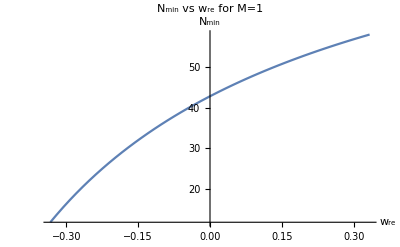

```mathematica
Show[%16,AxesLabel->{HoldForm[Subscript[w, re]],HoldForm[Subscript[N, min]]},PlotLabel->HoldForm[Subscript[N, min] vs Subscript[w, re] for M=1],LabelStyle->{GrayLevel[0]}]
```

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

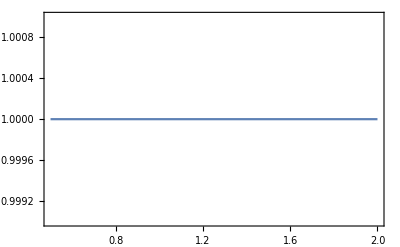

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.141056}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xyy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM 0.56419} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

-Graphics-

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

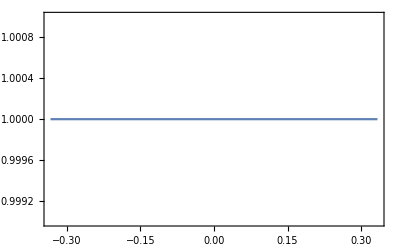

```mathematica
(*Consistency Checks*)
Plot[ϵ[θe[MM],MM],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}] (*I have total faith in this check passing, since it is a direct carry-over from the original code, and since that's not changed, this should still work fine*)
Plot[Nume[θN[Nm2[MM,0],MM],MM]/Nm2[MM,0],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}](*Here's the original consistency check with varying M, but w set at 0, for the second method*)
Plot[Nume[θN[Nm2[1,w],1],1]/Nm2[1,w],{w,wmin,wmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}]
(*Consistency check with varying w and holding M constant at 1*)
```

```mathematica
Nm2[1,1/3]
```

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xyy} is not a list of numbers with dimensions {1} at {xx} = {-0.282095}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,1]==xyy,{xx,θe[1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

57.9702

```mathematica
Nre[58.4625,1]
```

45.2539

```mathematica
Trh[48,1,0]//Timing
```

{0.522174,2.4904×10^6}

```mathematica
Trh[48,1,1/3]//Timing
```

{0.597515,2.33873}